```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
WPM=40;WPL=30;WPL=15;
(**)
```

```mathematica
q = 51; V0=(204/100)*10^(-8);
t0 = (q*(3*q-1)/V0)^(1/2);ϕ0=1; dϕ0=N[(((2*q)^(1/2))/t0),60];Ni=0;Nf=70;
```

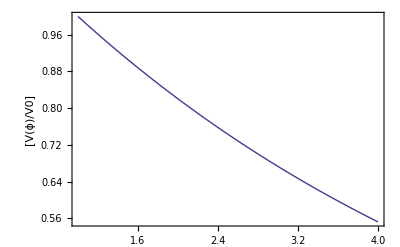

```mathematica
V[ϕ_] = V0*Exp[-((2/q)^(1/2))*(ϕ-ϕ0)];
DV[ϕ_] = D[V[ϕ],ϕ];
Plot[(V[ϕ]/V0),{ϕ,ϕ0,4},PlotRange->All,Frame->True, FrameLabel->{"[V(ϕ)/V0]"}]
```

```mathematica
H0 = ((1/3)*((dϕ0^2/2)+V[ϕ0]))^(1/2);
Dϕ0 = (dϕ0/H0);
```

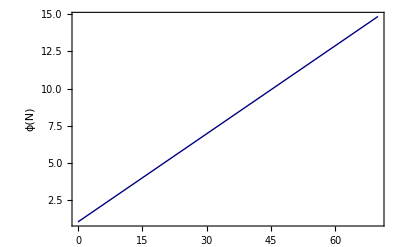

```mathematica
ϕSoln=NDSolve[{ϕ''[eN]+(3-ϕ'[eN]^2/2)*ϕ'[eN]+(DV[ϕ[eN]]/(2*V[ϕ[eN]]))*(6-(ϕ'[eN])^2)==0,ϕ[Ni]==ϕ0,ϕ'[Ni]==Dϕ0},ϕ,{eN,Ni,Nf},MaxSteps->1000000, WorkingPrecision->WPM];
ϕ[eN_]=ϕ[eN]/.Flatten[ϕSoln];
Plot[ϕ[eN],{eN,Ni,Nf},Frame->True,PlotRange->All,FrameLabel->{"ϕ(N)"},PlotStyle->{Darker[Blue,0.5]}]
```

```mathematica
toFile = Table[{" ",N[eN,10] ,N[ϕ[eN],10] ," "},{eN,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/mathematica_codes/phi_vs_N_mathematica.txt",toFile];
```

{{ ,0.,1., },{ ,0.0007,1.00014, },{ ,0.0014,1.00028, },«99995»,{ ,69.9986,14.8618, },{ ,69.9993,14.8619, },{ ,70.,14.8621, }}

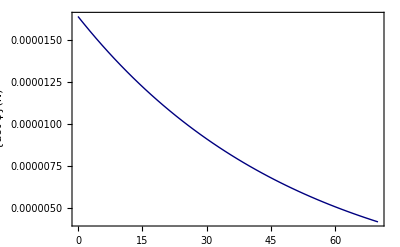

```mathematica
H[eN_]=(V[ϕ[eN]]/(3-((ϕ'[eN])^2)/2))^(1/2);
Plot[{H[eN]*ϕ'[eN]},{eN,Ni,Nf},Frame->True, PlotRange->All, FrameLabel->{"{dot ϕ}(N)"},PlotStyle->{Darker
[Blue,0.5]}]
```

```mathematica
toFile =Table[{" ",N[eN,10],N[H[eN],10]," "},{eN,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/mathematica_codes/H_vs_N_mathematica.txt",toFile];
```

{{ ,0.,0.0000827329, },{ ,0.0007,0.0000827318, },{ ,0.0014,0.0000827307, },«99996»,{ ,69.9993,0.0000209698, },{ ,70.,0.0000209695, }}

```mathematica
toFile = Table[{" ",N[eN,10],N[H'[eN]*10^6,10]," "},{eN,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/mathematica_codes/DH_vs_N_mathematica.txt",toFile];
```

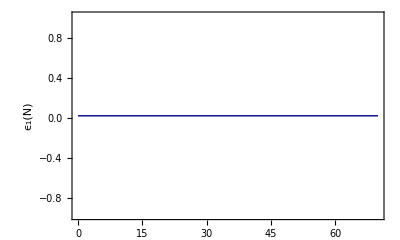

```mathematica
ϵ1[eN_] =((ϕ'[eN])^2/2);
Plot[ϵ1[eN],{eN,Ni,Nf},Frame->True, PlotRange->All, AspectRatio->0.6,FrameLabel->{"\!\(\*SubscriptBox[\(ϵ\),\(1\)]\)(N)"},PlotStyle->{Darker[Blue, 0.5]}]
```

```mathematica
toFile=Table[{" ",N[eN,10],N[ϵ1[eN],10]," "},{eN,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/mathematica_codes/eps_vs_N_mathematica.txt",toFile];
```

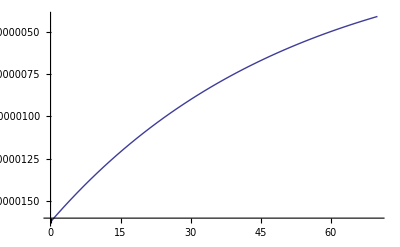

```mathematica
Plot[H'[eN],{eN,Ni,Nf}]
```